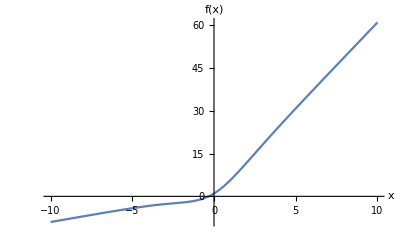

```mathematica
(* setup *)
ftrue[x_]:=1+x(1+5(1+E^(-x))^(-1)); (* modello "vero" dal quale si generano i dati *)
atrue=1; (* In realtà qualunque a > 0 si comporta nello stesso modo; questo è un po' il "problema" di questa funzione obiettivo, ma anche la feature che crea dei minimi con una grande differenza di curvature lungo b; ovviamente è stata scelta in maniera artificiale perché avesse sia minimi molto piccati che minimi molto piatti *)
btrue=5;
fmod[x_,a_,b_]:=x(1+b(1+E^(-a x))^(-1))+a^2; (* NOTA: puoi provare ad aggiungere questo termine a^2 come "penalità" per eliminare gli infiniti minimi con a>0 *)
losssingle[x_,y_,a_,b_]:=(y -fmod[x,a,b])^2; (* questa è solo la parte quadratica, senza somma o normalizzazione*)
gradloss[x_,y_,a_,b_]:={D[(y -fmod[x,a,b])^2,a],D[(y -fmod[x,a,b])^2,b]} ;
Plot[ftrue[x],{x,-10,10},AxesLabel->{"x","f(x)"}]
```

```mathematica
(* generate a sample from ftrue*)
nn=30;
ll=20;
ntot=nn ll; (*number of datapoints*)
xs = Table[xi-Floor[nn/2],{ xi,1,nn}];
fi=Table[N[ftrue[x/.(x->xs[[i]])]],{i,1,Length[xs]}];
eps=3;
epss = RandomReal[{-eps,eps},ll*Length[fi]];
data=Table[{xs[[i]],Table[fi[[i]]+epss[[i+j]],{j,0,ll-1}]},{i,1,Length[fi]}];

(******genero dati per l'errore di generalizzazione************)
nnp= Floor[N[nn/5]];
llp = Floor[N[ll/5]];
ntotp=nnp llp; (*number of datapoints*)
xsp = Table[xi-Floor[nnp/2],{ xi,1,nnp}];
fip=Table[N[ftrue[x/.(x->xsp[[i]])]],{i,1,Length[xsp]}];
epssp = RandomReal[{-eps,eps},llp*Length[fip]];
datap=Table[{xsp[[i]],Table[fip[[i]]+epssp[[i+j]],{j,0,llp-1}]},{i,1,Length[fip]}];
lossp[a_,b_]:=(1/ntotp)*Sum[ Sum[(datap[[i,2]][[j]]-fmod[datap[[i,1]],a,b])^2,{j,1,llp}],{i,1,nnp}];(*loss function per il validation set*)
(************************************************************)
```

```mathematica
loss[a_,b_]:=(1/ntot)* Sum[ Sum[(data[[i,2]][[j]]-fmod[data[[i,1]],a,b])^2,{j,1,ll}],{i,1,nn}];
areal=x/.Last[ FindMinimum[{loss[x,y],Abs[x]<=1.5atrue &&Abs[y]<=1btrue},{x,y}]];

breal=y/.Last[ FindMinimum[{loss[x,y],Abs[x]<=1.5 atrue &&Abs[y]<=1btrue},{x,y}]];
```

```mathematica
(*Trovo il minimo negativo della funzione*)
arealmin=x/.Last[ FindMinimum[{loss[x,y],x<0 },{x,y}]]

brealmin=y/.Last[ FindMinimum[{loss[x,y],x<0 },{x,y}]]
```

-5.64915

3.18288

```mathematica
(*cerco i punti in cui il gradiente si annulla*)
gradlosstot[a_,b_]:=(1/ntot)*Sum[Sum[gradloss[data[[i,1]],data[[i,2]][[j]],x,y],{j,1,ll}],{i,1,nn}]/.{x->a,y->b};
asaddleprecise=x/.FindRoot[{gradlosstot[x,y][[1]],gradlosstot[x,y][[2]]},{{x,-0.6},{y,25/6}}];
bsaddleprecise=y/.FindRoot[{gradlosstot[x,y][[1]],gradlosstot[x,y][[2]]},{{x,-0.6},{y,25/6}}];

hessloss[x_,y_,a_,b_]:= {{D[D[(y -fmod[x,a,b])^2,a],a],D[D[(y -fmod[x,a,b])^2,a],b]},{D[D[(y -fmod[x,a,b])^2,b],a],D[D[(y -fmod[x,a,b])^2,b],b]}};

hesslosssaddle= Sum[Sum[hessloss[data[[i,1]],data[[i,2]][[j]],x,y]/.{x->asaddleprecise,y->bsaddleprecise},{j,1,ll}],{i,1,nn}];
Print[Eigenvalues[hesslosssaddle]];
```

{-222381.,66881.3}

```mathematica
loss[1,2]
```

381.224

```mathematica
etaindex={0.0001,0.00008,0.00006,0.00004};
```

```mathematica
iterations=Table[0,{i,1,Length[etaindex]}];
bsizesgd =bsize=1;



(*calcolo l'hessiano, lo valuto su tutto il set e nel punto di minimo nello spazio dei parametri(che conosco)*)
hessloss[x_,y_,a_,b_]:= {{D[D[(y -fmod[x,a,b])^2,a],a],D[D[(y -fmod[x,a,b])^2,a],b]},{D[D[(y -fmod[x,a,b])^2,b],a],D[D[(y -fmod[x,a,b])^2,b],b]}};


(*valuto l'hessiano nel minimo reale*)
hesslossmin= Sum[Sum[hessloss[data[[i,1]],data[[i,2]][[j]],x,y]/.{x->areal,y->breal},{j,1,ll}],{i,1,nn}];
sqrthesslossmin=MatrixPower[ hesslossmin, 1/2];
(*calcolo il gradiente su tutto il set di dati*)
gradlosstot[a_,b_]:=(1/ntot)*Sum[Sum[gradloss[data[[i,1]],data[[i,2]][[j]],x,y],{j,1,ll}],{i,1,nn}]/.{x->a,y->b}

For[k=1,k≤ Length[etaindex],k++,
etasgd=etaindex[[k]];
timestep=etasgd;
vprev={arealmin,brealmin};
vcurrent=vprev;
Print["eta: ", etasgd];

ite=2;
While[vcurrent[[1]]<0.5||vcurrent[[2]]<4,
Z={RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]};
Zscale= sqrthesslossmin.Z;
vprev=vcurrent;
ai =vprev[[1]];
bi= vprev[[2]];
vcurrent[[1]]= ai-gradlosstot[x,y][[1]]*timestep+Sqrt[(2*etasgd/bsizesgd)*loss[x,y]]*Zscale[[1]]*Sqrt[timestep]/.{x->ai,y->bi};
vcurrent[[2]]= bi-gradlosstot[x,y][[2]]*timestep+Sqrt[(2*etasgd/bsizesgd)*loss[x,y]]*Zscale[[2]]*Sqrt[timestep]/.{x->ai,y->bi};
If[Mod[ite,100]==0, Print[ite, ", ", vcurrent]];
ite++;
];
iterations[[k]]=ite;
];
```

eta: 0.0001

100, {-6.14477,4.39847}

eta: 0.00008

100, {-8.14595,8.3993}

200, {-6.73363,18.146}

300, {-8.47876,10.6004}

400, {-4.91887,5.74476}

500, {-3.67927,1.15835}

600, {-6.34542,1.46294}

700, {-4.73764,0.0154681}

eta: 0.00006

100, {-4.36659,4.98363}

200, {-6.50988,3.62313}

300, {-4.71409,-2.46747}

400, {-6.63465,12.5562}

500, {-7.16144,4.88279}

600, {-5.21469,0.72382}

700, {-5.87575,0.183825}

800, {-3.97843,-2.45293}

900, {-5.35524,-4.39669}

1000, {-1.48028,4.50388}

1100, {-4.93047,-1.92304}

1200, {-5.80542,-6.34674}

1300, {-8.51124,-4.71763}

1400, {-4.64419,2.63086}

1500, {-6.07521,6.68774}

1600, {-4.9233,0.354945}

1700, {-3.75755,2.90496}

1800, {-3.34169,1.88946}

1900, {-2.13352,8.83105}

eta: 0.00004

100, {-4.89044,3.9681}

200, {-5.70993,4.5009}

300, {-5.7871,3.44502}

400, {-5.65771,2.94827}

500, {-6.57365,0.531792}

600, {-5.57421,3.27889}

700, {-4.42563,8.72826}

800, {-7.9623,6.43561}

900, {-6.05678,6.29598}

1000, {-6.41548,0.992534}

1100, {-5.31137,2.05838}

1200, {-3.89886,6.18876}

1300, {-6.55202,7.88837}

1400, {-6.63395,8.07417}

1500, {-7.47904,9.1801}

1600, {-7.30467,5.13792}

1700, {-5.96173,9.49583}

1800, {-8.3596,18.4361}

1900, {-9.32885,6.48095}

2000, {-6.97368,9.78714}

2100, {-6.65692,7.83573}

2200, {-6.45893,9.65281}

2300, {-7.18069,6.32536}

2400, {-7.80947,4.42837}

2500, {-7.48809,12.7176}

2600, {-6.72729,23.8239}

2700, {-8.40284,16.5746}

2800, {-7.08362,5.4454}

2900, {-6.54125,3.9203}

3000, {-5.52406,1.81858}

3100, {-5.13742,2.43282}

3200, {-5.05982,1.27167}

3300, {-4.27985,0.481305}

3400, {-4.48582,-1.12257}

3500, {-5.0716,0.437259}

3600, {-5.99578,2.33277}

3700, {-5.2616,2.19348}

3800, {-4.74523,1.29777}

3900, {-5.71419,3.15935}

4000, {-7.23949,-1.23165}

4100, {-5.57674,-0.0812849}

4200, {-4.41218,-7.0263}

4300, {-2.85371,-20.156}

4400, {7.34624,-20.1524}

4500, {5.72243,-1.87596}

4600, {5.96487,0.50548}

4700, {1.76065,-5.34285}

4800, {3.8817,-4.24937}

```mathematica
iterations={187,765,1911,4885}
```

{187,765,1911,4885}

```mathematica
{187,765,1911,4885}
```

```mathematica
etainverse=1/etaindex;
logesctime=(iterations*etaindex);
theocoeff=loss[asaddleprecise,bsaddleprecise]/loss[areal,breal]*bsize/Eigenvalues[hesslossmin][[1]]
etamean=0.00007;
derev=2 Pi /Sqrt[Eigenvalues[hesslossmin][[1]]*(-Eigenvalues[hesslosssaddle][[1]])]*(loss[asaddleprecise,bsaddleprecise]/loss[areal,breal])^(bsize/(Eigenvalues[hesslossmin][[1]]*etamean))+(-1/etamean^2)*Log[loss[asaddleprecise,bsaddleprecise]/loss[areal,breal]];

Print[derev]




simdata = Table[{etainverse[[i]],logesctime[[i]]},{i,1,Length[etainverse]}];
```

0.00836424

-1.24024×10^9

```mathematica
2
```

```mathematica
Eigenvalues[hesslossmin][[1]]
```

52101.5

```mathematica
1/Eigenvalues[hesslossmin][[1]]
```

0.0000193298

```mathematica
lm=LinearModelFit[simdata,x,x];
Normal[lm]
lun=Length[etainverse];
```

-0.0871111+0.0000115076 x

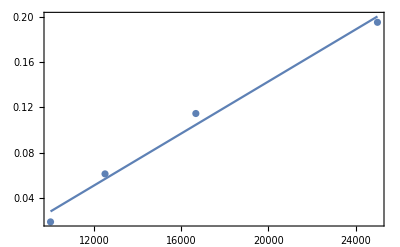

```mathematica
Show[ListPlot[simdata],Plot[lm[x],{x,etainverse[[1]],etainverse[[lun]]},Axes->True,AxesLabel->{"learning rate","escape time"}],Frame->True,PlotRange->All]
```

```mathematica
nlm=NonlinearModelFit[simdata,c*loss[asaddleprecise,bsaddleprecise]^(d/x),{c,d},x];
```

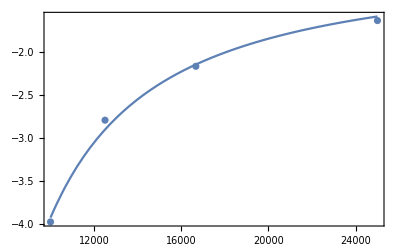

```mathematica
Show[ListPlot[simdata],Plot[nlm[x],{x,etainverse[[1]],etainverse[[lun]]}],Frame->True,PlotRange->All]
```

```mathematica
nlm["BestFitParameters"]
```

{c→-0.865102,d→2167.03}